```mathematica
datapath = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\Zurich Instruments\\";
importdataFolders = FileNames["Board*",datapath];
importdata = Table[Import[#,"Table"]&/@(FileNames["\\*.txt",importdataFolders[[board]]]),{board,1,Dimensions[importdataFolders][[1]]}];

datapathOld = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\MLA Data\\Single_Board_2_221021\\";
importdataOld = Import[#,"Table"]&/@(FileNames[datapathOld<>"\\*.txt"]);

datapathNew = "C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\Zurich Instruments\\New Board 2\\";
importdataNew = Import[#,"Table"]&/@(FileNames[datapathNew<>"\\*.txt"]);
```

```mathematica
p1=Flatten[Table[{{5-p,5-q,2},{5-p,5-q,1}},{p,1,4},{q,1,4}],2];
p2=Flatten[Table[{{9-p,5-q,2},{9-p,5-q,1}},{p,1,4},{q,1,4}],2];
p3=Flatten[Table[{{4+p,4+q,1},{4+p,4+q,2}},{p,1,4},{q,1,4}],2];
p4=Flatten[Table[{{p,4+q,1},{p,4+q,2}},{p,1,4},{q,1,4}],2];
correspondingNodeCoords=Join[p1,p2,p3,p4];

boards = {1,2,3,4,5};

RShunt = 10;
```

```mathematica
importdata//Dimensions
```

{4,256,506}

```mathematica
frequencies = Table[(ToExpression[StringDelete[importdata[[1,2*j-1,6+i,1]],","]]),{j,1,Dimensions[importdata][[2]]/2},{i,1,Length[importdata[[1,1,7;;,-1]]]}];

voltage1 = Table[(ToExpression[StringDelete[importdata[[board,2*j-1,6+i,2]],","]])*Exp[-I*2π*(ToExpression[importdata[[board,2*j-1,6+i,3]]])/360],{board,1,Dimensions[importdata][[1]]},{j,1,Dimensions[importdata][[2]]/2},{i,1,Length[importdata[[1,1,7;;,-1]]]}];

voltage2 = Table[(ToExpression[StringDelete[importdata[[board,2*j,6+i,2]],","]])*Exp[-I*2π*(ToExpression[importdata[[board,2*j,6+i,3]]])/360],{board,1,Dimensions[importdata][[1]]},{j,1,Dimensions[importdata][[2]]/2},{i,1,Length[importdata[[1,1,7;;,-1]]]}];

absImpedance = Table[{frequencies[[Position[correspondingNodeCoords,{x,y,sub}][[1,1]],i]],Abs[(voltage1[[board,Position[correspondingNodeCoords,{x,y,sub}][[1,1]],i]])*RShunt/((voltage2[[board,Position[correspondingNodeCoords,{x,y,sub}][[1,1]],i]]))]},{x,1,8,1},{y,1,8,1},{board,1,Dimensions[importdata][[1]],1},{sub,1,2,1},{i,1,Length[importdata[[1,1,7;;,-1]]]}];

argImpedance = Table[{frequencies[[Position[correspondingNodeCoords,{x,y,sub}][[1,1]],i]],-Arg[(voltage1[[board,Position[correspondingNodeCoords,{x,y,sub}][[1,1]],i]])*RShunt/(-(voltage2[[board,Position[correspondingNodeCoords,{x,y,sub}][[1,1]],i]]))]},{x,1,8,1},{y,1,8,1},{board,1,Dimensions[importdata][[1]],1},{sub,1,2,1},{i,1,Length[importdata[[1,1,7;;,-1]]]}];
```

```mathematica
(*Sorts imported data into the format: {Board,j node,{Ampitude V1,Ampitude V2,Phase V1,Phase V2},1000 Measurement Points of the Sweep,{Frequency,Value}}*)
voltageDataOld= Table[importdataOld[[j,(entry-1)*999+entry*4;;(entry)*999+entry*4]],{j,1,Dimensions[importdataOld][[1]]},{entry,1,4}];
(*Sorts imported data into the format: {j node, 1000 Measurement Points of the Sweep,{Frequency, Amplitude V1, Phase V1}}*)
voltage1JOld = Table[Transpose[{voltageDataOld[[j,1,;;,1]]*1000,voltageDataOld[[j,1,;;,2]],voltageDataOld[[j,3,;;,2]]}],{j,1,Dimensions[importdataOld][[1]]}];
(*Sorts imported data into the format: {j node, 1000 Measurement Points of the Sweep,{Frequency, Amplitude V2, Phase V2}}*)
voltage2JOld = Table[Transpose[{voltageDataOld[[j,1,;;,1]]*1000,voltageDataOld[[j,2,;;,2]],voltageDataOld[[j,4,;;,2]]}],{j,1,Dimensions[importdataOld][[1]]}];

frequencyArray = voltage1JOld[[1,;;,1]];

impedancesJOrderedOld = Table[{frequencyArray[[freq]],(RShunt*(voltage2JOld[[j,freq,2]])*Exp[I(voltage2JOld[[j,freq,3]])*2π/360])/(((voltage1JOld[[j,freq,2]])*Exp[I(voltage1JOld[[j,freq,3]])*2π/360])-((voltage2JOld[[j,freq,2]])*Exp[I(voltage2JOld[[j,freq,3]])*2π/360]))},{j,1,Dimensions[importdataOld][[1]]},{freq,1,Length[frequencyArray]}];

ImpedancesArrayOld = Table[Abs[impedancesJOrderedOld[[Position[correspondingNodeCoords,{x,y,sub}][[1,1]]]]],{x,1,8},{y,1,8},{sub,1,2}];


voltage1JNew = Table[(ToExpression[StringDelete[importdataNew[[2*j-1,6+i,2]],","]])*Exp[-I*2π*(ToExpression[importdataNew[[2*j-1,6+i,3]]])/360],{j,1,Dimensions[importdataNew][[1]]/2},{i,1,Length[importdataNew[[1,7;;,-1]]]}];

voltage2JNew = Table[(ToExpression[StringDelete[importdataNew[[2*j,6+i,2]],","]])*Exp[-I*2π*(ToExpression[importdataNew[[2*j,6+i,3]]])/360],{j,1,Dimensions[importdataNew][[1]]/2},{i,1,Length[importdataNew[[1,7;;,-1]]]}];

impedancesJOrderedNew = Table[{frequencies[[1,freq]],(RShunt*(voltage1JNew[[j,freq]]))/(((voltage2JNew[[j,freq]])))},{j,1,Dimensions[voltage1JNew][[1]]},{freq,1,Length[importdataNew[[1,7;;,-1]]]}];
```

```mathematica
Manipulate[ListLinePlot[absImpedance[[x,y,board,sub]],PlotRange->All,PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[ y]<>"," <>ToString[boards[[board]]]<>","<> ToString[If[sub==1,A,B]]<>")",AxesLabel->{"Resistance in Ω","Frequency in Hz"}],{x,1,8,1},{y,1,8,1},{board,1,Dimensions[importdata][[1]],1},{sub,1,2,1},SaveDefinitions->True]

Manipulate[ListLinePlot[argImpedance[[x,y,board,sub]],PlotRange->All,PlotLabel->"Node: ("<>ToString[x]<>","<>ToString[ y]<>"," <>ToString[boards[[board]]]<>","<> ToString[If[sub==1,A,B]]<>")",AxesLabel->{"Resistance in Ω","Frequency in Hz"}],{x,1,8,1},{y,1,8,1},{board,1,Dimensions[importdata][[1]],1},{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
meanAbs = Table[Mean[Flatten[absImpedance[[;;,;;,;;,sub,i,2]]]],{sub,1,2},{i,1,Length[importdata[[1,1,7;;,-1]]]}];

meanArg = Table[Mean[Flatten[argImpedance[[;;,;;,;;,sub,i,2]]]],{sub,1,2},{i,1,Length[importdata[[1,1,7;;,-1]]]}];
```

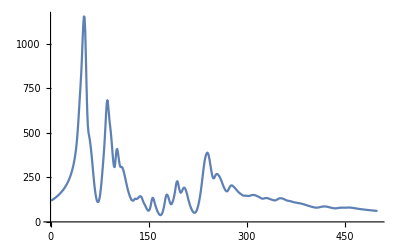

```mathematica
ListLinePlot[meanAbs[[2]],PlotRange->All]
```

```mathematica
interpolationVoltagesOld = Table[Interpolation[Abs[ImpedancesArrayOld[[x,y,sub]]]],{x,1,8},{y,1,8},{sub,1,2}];

interpolationVoltagesNew = Table[Interpolation[Abs[impedancesJOrderedNew[[j]]]],{j,1,Dimensions[voltage1JNew][[1]]}];
```

```mathematica
completeInterpolation = Table[Which[x==1,
Which[y==7 ,interpolationVoltagesNew[[sub]],y==8,interpolationVoltagesNew[[2+sub]],True,interpolationVoltagesOld[[x,y,sub]]],
True,interpolationVoltagesOld[[x,y,sub]]
],{x,1,8},{y,1,8},{sub,1,2}];
```

```mathematica
meanOld = Table[Mean[Flatten[Table[interpolationVoltagesOld[[x,y,sub]][frequencies[[1,freq]]],{x,1,8},{y,1,8}]]],{sub,1,2},{freq,1,Length[importdataNew[[1,7;;,-1]]]}];

meanNew2 = Table[Mean[Flatten[Table[completeInterpolation[[x,y,sub]][frequencies[[1,freq]]],{x,1,8},{y,1,8}]]],{sub,1,2},{freq,1,Length[importdataNew[[1,7;;,-1]]]}];
```

InterpolatingFunction::dmval: Input value {5.×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {5.×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
peakSubABPosVals = Table[{Position[meanAbs,Max[meanAbs[[1,If[freqs==1,130;;250,173]]]]][[1,2]], Position[meanAbs,Max[meanAbs[[2,If[freqs==1,130;;250,173]]]]][[1,2]]},{freqs,1,2}];

deviationOfNodesNew2 = Table[Block[{peakSubABPos = peakSubABPosVals},(Max[completeInterpolation[[x,y,sub]][frequencies[[1,peakSubABPos[[freqs,sub]]]]]]-meanNew2[[sub,peakSubABPos[[freqs,sub]]]])/(meanNew2[[sub,peakSubABPos[[freqs,sub]]]])],{freqs,1,2},{x,1,8},{y,1,8},{sub,1,2}];

deviationOfNodesBoard2 = Table[Block[{peakSubABPos = peakSubABPosVals},(Max[interpolationVoltagesOld[[x,y,sub]][frequencies[[1,peakSubABPos[[freqs,sub]]]]]]-meanOld[[sub,peakSubABPos[[freqs,sub]]]])/(meanOld[[sub,peakSubABPos[[freqs,sub]]]])],{freqs,1,2},{x,1,8},{y,1,8},{sub,1,2}];

completeDeviationBoard2 = Table[If[board==1,deviationOfNodesBoard2,deviationOfNodesNew2],{board,1,2}];
```

```mathematica
deviationHistOldVSNew = Table[DiscretePlot3D[Abs[completeDeviationOfNodes[[board,freqs,x,y,sub]]],{x,1,8},{y,1,8},ExtentSize->Full,FillingStyle->Opacity[0.7],PlotRange->{All,All,{0,0.5}},TicksStyle->White,Ticks->{cellsHistMulti,cellsHistMulti,{{0,"0"},{0.3,"20"},{0.5,"40"}}},ColorFunction->Function[{x,y,z},RGBColor[z^2,0,0]],AxesLabel->{"x-Axis","y-Axis","Deviation in %"},AxesStyle->White,FaceGrids->All,ViewPoint->{-1,-1,1.5},PlotLabel->Style["Deviation from mean value in % of sublattice "<>ToString[If[sub==1,A,B]]<>" of board "<>ToString[board]<>" at "<>ToString[freqLabels[[freqs,sub]]]<>" MHz",White],ImageSize->400,Background->Black],{freqs,1,2},{board,1,Dimensions[completeDeviationBoard2][[1]]},{sub,1,2}];
```

```mathematica
deviationOfNodes = Table[Block[{peakSubABPos = peakSubABPosVals},(Max[Abs[absImpedance[[x,y,board,sub,peakSubABPos[[freqs,sub]],2]]]]-meanAbs[[sub,peakSubABPos[[freqs,sub]]]])/(meanAbs[[sub,peakSubABPos[[freqs,sub]]]])],{freqs,1,2},{x,1,8},{y,1,8},{board,1,Dimensions[importdata][[1]],1},{sub,1,2}];
```

```mathematica
completeDeviationOfNodes = Table[If[board!=2,deviationOfNodes[[;;,;;,;;,Which[board< 2,board,board>2,board-1,True,0],;;]],deviationOfNodesBoard2]
,{board,1,Dimensions[importdata][[1]]+1,1}];
```

```mathematica
Manipulate[MatrixForm[Reverse[Transpose[completeDeviationOfNodes[[board,freq,;;,;;,sub]]]]],{freq,1,2,1},{board,1,Dimensions[completeDeviationOfNodes][[1]],1},{sub,1,2,1},SaveDefinitions->True];
```

```mathematica
deviationOfNodes//Dimensions
completeDeviationOfNodes//Dimensions
```

{2,8,8,4,2}

{5,2,8,8,2}

```mathematica
stdNodes = Table[StandardDeviation[deviationOfNodes[[freq,x,y,;;,sub]]],{freq,1,2,1},{x,1,8,1},{y,1,8,1},{sub,1,2,1}];

completeStdNodes = Table[StandardDeviation[completeDeviationOfNodes[[;;,freq,x,y,sub]]],{freq,1,2,1},{x,1,8,1},{y,1,8,1},{sub,1,2,1}];

Manipulate[MatrixForm[Reverse[Transpose[stdNodes[[freq,;;,;;,sub]]]]],{freq,1,2,1},{sub,1,2,1},SaveDefinitions->True];

Manipulate[MatrixForm[Reverse[Transpose[completeStdNodes[[freq,;;,;;,sub]]]]],{freq,1,2,1},{sub,1,2,1},SaveDefinitions->True]
```

```mathematica
cellsHistMulti =Table[{i,i},{i,8}];

freqLabels = {{1.97,1.69},{2.38,2.38}};

deviationHist = Table[DiscretePlot3D[Abs[completeDeviationOfNodes[[board,freqs,x,y,sub]]],{x,1,8},{y,1,8},ExtentSize->Full,FillingStyle->Opacity[0.7],PlotRange->{All,All,{0,0.5}},TicksStyle->White,Ticks->{cellsHistMulti,cellsHistMulti,{{0,"0"},{0.3,"20"},{0.5,"40"}}},ColorFunction->Function[{x,y,z},RGBColor[z^2,0,0]],AxesLabel->{"x-Axis","y-Axis","Deviation in %"},AxesStyle->White,FaceGrids->All,ViewPoint->{-1,-1,1.5},PlotLabel->Style["Deviation from mean value in % of sublattice "<>ToString[If[sub==1,A,B]]<>" of board "<>ToString[board]<>" at "<>ToString[freqLabels[[freqs,sub]]]<>" MHz",White],ImageSize->400,Background->Black],{freqs,1,2},{board,1,Dimensions[completeDeviationOfNodes][[1]]},{sub,1,2}];
```

```mathematica
Manipulate[deviationHist[[freqs,board,sub]],{freqs,1,2,1},{board,1,Dimensions[completeDeviationOfNodes][[1]],1},{sub,1,2,1},ControlType->VerticalSlider,SaveDefinitions->True];
```

```mathematica
SetDirectory["C:\\Users\\Nelson's Laptop\\OneDrive - Universität Zürich UZH\\University\\Master\\Coding\\Exported Data"];
```

SetDirectory::cdir: Cannot set current directory to C:\Users\Nelson's Laptop\OneDrive - Universität Zürich UZH\University\Master\Coding\Exported Data.

```mathematica
Export["completeDeviationOfNodes.mx",completeDeviationOfNodes,"String","FieldSeparators"->" "];
Export["completeDeviationBoard2.mx",deviationHist,"String","FieldSeparators"->" "];
```

```mathematica
completeDeviationOfNodes//Dimensions
completeDeviationBoard2//Dimensions

completeDeviationOfNodes[[1,1,1,1,1]]
completeDeviationBoard2[[1,1,1,1,1]]
```

{5,2,8,8,2}

{2,2,8,8,2}

-0.334739

-0.251705